```mathematica
ClearAll[H,H1,Ht]
```

```mathematica
ρ=DiagonalMatrix[{1,0,0,0}];
```

```mathematica
cm[A_,B_]:=A.B-B.A;
am[A_,B_]:=A.B+B.A;
```

```mathematica
TrB[X_]:=Map[Tr,Partition[X,{2,2}],{2}]
```

```mathematica
{σ[0],σ[1],σ[2],σ[3]}=Table[PauliMatrix[i]/√2,{i,0,3}];
```

```mathematica
σ[1]
```

{{0,1/(√2)},{1/(√2),0}}

```mathematica
√2 Sum[σ[i] Subscript[B, i],{i,1,3}]//Simplify//MatrixForm
```

(B_3 | B_1-ⅈ B_2
B_1+ⅈ B_2 | -B_3)

```mathematica
{B[0],B[1],B[2],B[3]}=Array[Subscript[b, #1,#2]&,{4,4},0].Table[σ[i],{i,0,3}]/.Subscript[b, 0,0]->0;
Ω0=Sum[KroneckerProduct[σ[i],B[i]],{i,0,3}]//ComplexExpand;
MatrixForm[Ω0]
```

((b_(0,3))/2+(b_(3,0))/2+(b_(3,3))/2 | (b_(0,1))/2+(b_(3,1))/2+ⅈ (-(b_(0,2))/2-(b_(3,2))/2) | (b_(1,0))/2+(b_(1,3))/2+ⅈ (-(b_(2,0))/2-(b_(2,3))/2) | (b_(1,1))/2+ⅈ (-(b_(1,2))/2-(b_(2,1))/2)-(b_(2,2))/2
(b_(0,1))/2+(b_(3,1))/2+ⅈ ((b_(0,2))/2+(b_(3,2))/2) | -(b_(0,3))/2+(b_(3,0))/2-(b_(3,3))/2 | (b_(1,1))/2+ⅈ ((b_(1,2))/2-(b_(2,1))/2)+(b_(2,2))/2 | (b_(1,0))/2-(b_(1,3))/2+ⅈ (-(b_(2,0))/2+(b_(2,3))/2)
(b_(1,0))/2+(b_(1,3))/2+ⅈ ((b_(2,0))/2+(b_(2,3))/2) | (b_(1,1))/2+ⅈ (-(b_(1,2))/2+(b_(2,1))/2)+(b_(2,2))/2 | (b_(0,3))/2-(b_(3,0))/2-(b_(3,3))/2 | (b_(0,1))/2-(b_(3,1))/2+ⅈ (-(b_(0,2))/2+(b_(3,2))/2)
(b_(1,1))/2+ⅈ ((b_(1,2))/2+(b_(2,1))/2)-(b_(2,2))/2 | (b_(1,0))/2-(b_(1,3))/2+ⅈ ((b_(2,0))/2-(b_(2,3))/2) | (b_(0,1))/2-(b_(3,1))/2+ⅈ ((b_(0,2))/2-(b_(3,2))/2) | -(b_(0,3))/2-(b_(3,0))/2+(b_(3,3))/2)

```mathematica
Sum[Tr[B[i].B[i]],{i,1,3}]//Simplify
```

b_(1,0)^2+b_(1,1)^2+b_(1,2)^2+b_(1,3)^2+b_(2,0)^2+b_(2,1)^2+b_(2,2)^2+b_(2,3)^2+b_(3,0)^2+b_(3,1)^2+b_(3,2)^2+b_(3,3)^2

```mathematica
B1[0]=4B[0];
B1[1]=-4ⅈ cm[B[0],B[1]]//Simplify;
B1[2]=-2ⅈ cm[B[0],B[2]]+2am[B[1],B[3]]//Simplify;
B1[3]=0IdentityMatrix[2];
```

```mathematica
Ω1=Sum[KroneckerProduct[σ[i],B1[i]],{i,0,3}]//Simplify;
MatrixForm[Ω1]
```

(2 (b_(0,0)+b_(0,3)) | 2 (b_(0,1)-ⅈ b_(0,2)) | (b_(0,2) (-4 b_(1,1)+2 ⅈ b_(2,1))+b_(0,1) (4 b_(1,2)-2 ⅈ b_(2,2))-2 ⅈ (b_(1,1) b_(3,1)+b_(1,2) b_(3,2)+b_(1,0) (b_(3,0)+b_(3,3))+b_(1,3) (b_(3,0)+b_(3,3))))/(√2) | √2 (2 b_(0,2) b_(1,3)+b_(0,3) (-2 ⅈ b_(1,1)-2 b_(1,2)-b_(2,1)+ⅈ b_(2,2))-ⅈ b_(0,2) b_(2,3)+b_(0,1) (2 ⅈ b_(1,3)+b_(2,3))-ⅈ b_(1,1) b_(3,0)-b_(1,2) b_(3,0)-ⅈ b_(1,0) b_(3,1)-b_(1,0) b_(3,2))
2 (b_(0,1)+ⅈ b_(0,2)) | 2 (b_(0,0)-b_(0,3)) | √2 (2 b_(0,2) b_(1,3)+b_(0,3) (2 ⅈ b_(1,1)-2 b_(1,2)+b_(2,1)+ⅈ b_(2,2))+b_(0,1) (-2 ⅈ b_(1,3)-b_(2,3))-ⅈ b_(0,2) b_(2,3)-ⅈ b_(1,1) b_(3,0)+b_(1,2) b_(3,0)-ⅈ b_(1,0) b_(3,1)+b_(1,0) b_(3,2)) | (b_(0,2) (4 b_(1,1)-2 ⅈ b_(2,1))+b_(0,1) (-4 b_(1,2)+2 ⅈ b_(2,2))-2 ⅈ (b_(1,1) b_(3,1)+b_(1,2) b_(3,2)+b_(1,0) (b_(3,0)-b_(3,3))+b_(1,3) (-b_(3,0)+b_(3,3))))/(√2)
(-2 b_(0,2) (2 b_(1,1)+ⅈ b_(2,1))+b_(0,1) (4 b_(1,2)+2 ⅈ b_(2,2))+2 ⅈ (b_(1,1) b_(3,1)+b_(1,2) b_(3,2)+b_(1,0) (b_(3,0)+b_(3,3))+b_(1,3) (b_(3,0)+b_(3,3))))/(√2) | √2 (2 b_(0,2) b_(1,3)+b_(0,3) (-2 ⅈ b_(1,1)-2 b_(1,2)+b_(2,1)-ⅈ b_(2,2))+b_(0,1) (2 ⅈ b_(1,3)-b_(2,3))+ⅈ b_(0,2) b_(2,3)+ⅈ b_(1,1) b_(3,0)+b_(1,2) b_(3,0)+ⅈ b_(1,0) b_(3,1)+b_(1,0) b_(3,2)) | 2 (b_(0,0)+b_(0,3)) | 2 (b_(0,1)-ⅈ b_(0,2))
√2 (2 b_(0,2) b_(1,3)+b_(0,3) (2 ⅈ b_(1,1)-2 b_(1,2)-b_(2,1)-ⅈ b_(2,2))+ⅈ b_(0,2) b_(2,3)+b_(0,1) (-2 ⅈ b_(1,3)+b_(2,3))+ⅈ b_(1,1) b_(3,0)-b_(1,2) b_(3,0)+ⅈ b_(1,0) b_(3,1)-b_(1,0) b_(3,2)) | (b_(0,2) (4 b_(1,1)+2 ⅈ b_(2,1))-2 b_(0,1) (2 b_(1,2)+ⅈ b_(2,2))+2 ⅈ (b_(1,1) b_(3,1)+b_(1,2) b_(3,2)+b_(1,0) (b_(3,0)-b_(3,3))+b_(1,3) (-b_(3,0)+b_(3,3))))/(√2) | 2 (b_(0,1)+ⅈ b_(0,2)) | 2 (b_(0,0)-b_(0,3)))

```mathematica
Tr[B1[0].B1[0]]//Simplify
```

16 (b_(0,0)^2+b_(0,1)^2+b_(0,2)^2+b_(0,3)^2)

```mathematica
Sum[Tr[B1[i].B1[i]],{i,1,2}]/.{Subscript[b, 2,0]->0,Subscript[b, 2,1]->0,Subscript[b, 2,2]->0,Subscript[b, 2,3]->0}//Simplify
```

2 ((4 b_(0,2) b_(1,1)-4 b_(0,1) b_(1,2))^2+(4 ⅈ b_(0,3) (b_(1,1)+ⅈ b_(1,2))+4 (-ⅈ b_(0,1)+b_(0,2)) b_(1,3)) (b_(0,3) (-4 ⅈ b_(1,1)-4 b_(1,2))+4 (ⅈ b_(0,1)+b_(0,2)) b_(1,3))+4 (b_(1,1) b_(3,0)-ⅈ b_(1,2) b_(3,0)+b_(1,0) (b_(3,1)-ⅈ b_(3,2))) (b_(1,1) b_(3,0)+ⅈ b_(1,2) b_(3,0)+b_(1,0) (b_(3,1)+ⅈ b_(3,2)))+2 (b_(1,1) b_(3,1)+b_(1,2) b_(3,2)+b_(1,0) (b_(3,0)-b_(3,3))+b_(1,3) (-b_(3,0)+b_(3,3)))^2+2 (b_(1,1) b_(3,1)+b_(1,2) b_(3,2)+b_(1,0) (b_(3,0)+b_(3,3))+b_(1,3) (b_(3,0)+b_(3,3)))^2)

```mathematica
sol=NMaximize[{Sum[Tr[B1[i].B1[i]],{i,1,2}],
Subscript[b, 0,1]^2+Subscript[b, 0,2]^2+Subscript[b, 0,3]^2≤ 0.001
&&Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2+Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2+Subscript[b, 3,0]^2+Subscript[b, 3,1]^2+Subscript[b, 3,2]^2+Subscript[b, 3,3]^2≤ 0.01},
{Subscript[b, 0,1],Subscript[b, 0,2],Subscript[b, 0,3],Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3],Subscript[b, 2,0],Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3],Subscript[b, 3,0],Subscript[b, 3,1],Subscript[b, 3,2],Subscript[b, 3,3]}]
```

{0.000521709+0. ⅈ,{b_(0,1)→-0.0134055,b_(0,2)→0.0184279,b_(0,3)→0.021925,b_(1,0)→0.0404237,b_(1,1)→-0.0359441,b_(1,2)→0.0266084,b_(1,3)→-0.0443413,b_(2,0)→-3.63101×10^-6,b_(2,1)→0.010321,b_(2,2)→0.0101812,b_(2,3)→-0.00224605,b_(3,0)→0.0462207,b_(3,1)→-0.0258301,b_(3,2)→0.0191222,b_(3,3)→-0.0318648}}

```mathematica
B[0]/.sol[[2]]
```

{{0.0388332,-0.0558171+0.0194018 ⅈ},{-0.0558171-0.0194018 ⅈ,-0.0388332}}

```mathematica
B[1]/.sol[[2]]
```

{{-0.0391099,-0.0416805-0.0416312 ⅈ},{-0.0416805+0.0416312 ⅈ,0.0391099}}

```mathematica
Norm[cm[B[0],B[1]]/.sol[[2]],"Frobenius"]^2
```

7.93226×10^-6

```mathematica
Norm[B[3]/.sol[[2]],"Frobenius"]^2
```

0.00418457

```mathematica
pl0pp0-iop;p;p
```

```mathematica
ll
```

```mathematica
m,.,
```

```mathematica
CMDD2=TrB[Nest[cm[HtDD,#]&,ρ,2]][[1,1]]//ComplexExpand
```

32 b_(0,2)^2 b_(1,1)^2+32 b_(0,3)^2 b_(1,1)^2-64 b_(0,1) b_(0,2) b_(1,1) b_(1,2)+32 b_(0,1)^2 b_(1,2)^2+32 b_(0,3)^2 b_(1,2)^2-64 b_(0,1) b_(0,3) b_(1,1) b_(1,3)-64 b_(0,2) b_(0,3) b_(1,2) b_(1,3)+32 b_(0,1)^2 b_(1,3)^2+32 b_(0,2)^2 b_(1,3)^2+32 b_(0,3)^2 b_(1,2) b_(2,1)-32 b_(0,2) b_(0,3) b_(1,3) b_(2,1)+8 b_(0,2)^2 b_(2,1)^2+8 b_(0,3)^2 b_(2,1)^2-32 b_(0,3)^2 b_(1,1) b_(2,2)+32 b_(0,1) b_(0,3) b_(1,3) b_(2,2)-16 b_(0,1) b_(0,2) b_(2,1) b_(2,2)+8 b_(0,1)^2 b_(2,2)^2+8 b_(0,3)^2 b_(2,2)^2+32 b_(0,2) b_(0,3) b_(1,1) b_(2,3)-32 b_(0,1) b_(0,3) b_(1,2) b_(2,3)-16 b_(0,1) b_(0,3) b_(2,1) b_(2,3)-16 b_(0,2) b_(0,3) b_(2,2) b_(2,3)+8 b_(0,1)^2 b_(2,3)^2+8 b_(0,2)^2 b_(2,3)^2+32 b_(0,3) b_(1,1)^2 b_(3,0)+32 b_(0,3) b_(1,2)^2 b_(3,0)-32 b_(0,1) b_(1,1) b_(1,3) b_(3,0)-32 b_(0,2) b_(1,2) b_(1,3) b_(3,0)-16 b_(0,2) b_(1,0) b_(2,1) b_(3,0)+16 b_(0,3) b_(1,2) b_(2,1) b_(3,0)-16 b_(0,2) b_(1,3) b_(2,1) b_(3,0)+16 b_(0,1) b_(1,0) b_(2,2) b_(3,0)-16 b_(0,3) b_(1,1) b_(2,2) b_(3,0)+16 b_(0,1) b_(1,3) b_(2,2) b_(3,0)+16 b_(0,2) b_(1,1) b_(2,3) b_(3,0)-16 b_(0,1) b_(1,2) b_(2,3) b_(3,0)+8 b_(1,0)^2 b_(3,0)^2+8 b_(1,1)^2 b_(3,0)^2+8 b_(1,2)^2 b_(3,0)^2+16 b_(1,0) b_(1,3) b_(3,0)^2+8 b_(1,3)^2 b_(3,0)^2+32 b_(0,3) b_(1,0) b_(1,1) b_(3,1)-32 b_(0,1) b_(1,0) b_(1,3) b_(3,1)-16 b_(0,2) b_(1,1) b_(2,1) b_(3,1)-16 b_(0,3) b_(1,0) b_(2,2) b_(3,1)+16 b_(0,1) b_(1,1) b_(2,2) b_(3,1)+16 b_(0,2) b_(1,0) b_(2,3) b_(3,1)+32 b_(1,0) b_(1,1) b_(3,0) b_(3,1)+16 b_(1,1) b_(1,3) b_(3,0) b_(3,1)+8 b_(1,0)^2 b_(3,1)^2+8 b_(1,1)^2 b_(3,1)^2+32 b_(0,3) b_(1,0) b_(1,2) b_(3,2)-32 b_(0,2) b_(1,0) b_(1,3) b_(3,2)+16 b_(0,3) b_(1,0) b_(2,1) b_(3,2)-16 b_(0,2) b_(1,2) b_(2,1) b_(3,2)+16 b_(0,1) b_(1,2) b_(2,2) b_(3,2)-16 b_(0,1) b_(1,0) b_(2,3) b_(3,2)+32 b_(1,0) b_(1,2) b_(3,0) b_(3,2)+16 b_(1,2) b_(1,3) b_(3,0) b_(3,2)+16 b_(1,1) b_(1,2) b_(3,1) b_(3,2)+8 b_(1,0)^2 b_(3,2)^2+8 b_(1,2)^2 b_(3,2)^2-16 b_(0,2) b_(1,0) b_(2,1) b_(3,3)-16 b_(0,2) b_(1,3) b_(2,1) b_(3,3)+16 b_(0,1) b_(1,0) b_(2,2) b_(3,3)+16 b_(0,1) b_(1,3) b_(2,2) b_(3,3)+16 b_(1,0)^2 b_(3,0) b_(3,3)+32 b_(1,0) b_(1,3) b_(3,0) b_(3,3)+16 b_(1,3)^2 b_(3,0) b_(3,3)+16 b_(1,0) b_(1,1) b_(3,1) b_(3,3)+16 b_(1,1) b_(1,3) b_(3,1) b_(3,3)+16 b_(1,0) b_(1,2) b_(3,2) b_(3,3)+16 b_(1,2) b_(1,3) b_(3,2) b_(3,3)+8 b_(1,0)^2 b_(3,3)^2+16 b_(1,0) b_(1,3) b_(3,3)^2+8 b_(1,3)^2 b_(3,3)^2

```mathematica
TrB[Nest[cm[H,#]&,ρ,2]][[1,1]]
```

2 h_(1,3) h_(3,1)+2 h_(1,4) h_(4,1)

```mathematica
CMDD2h=Simplify[(CMDD2/.b2h)]
```

8 (-h_(1,2) h_(1,3) h_(2,1) h_(2,4)+2 h_(1,2) h_(2,1) h_(2,4)^2+h_(1,2) h_(1,3) h_(2,1) h_(3,1)-2 h_(1,2) h_(2,1) h_(2,4) h_(3,1)+4 h_(1,2) h_(2,1) h_(2,3) h_(3,2)-2 h_(1,2) h_(1,3) h_(2,3) h_(3,3)-2 h_(1,2) h_(2,3) h_(3,1) h_(3,3)-2 h_(1,3) h_(2,1) h_(3,2) h_(3,3)-2 h_(2,1) h_(3,1) h_(3,2) h_(3,3)+h_(1,3)^2 h_(3,3)^2+2 h_(1,3) h_(3,1) h_(3,3)^2+h_(3,1)^2 h_(3,3)^2-2 h_(1,2) h_(2,3)^2 h_(3,4)-2 h_(1,3) h_(2,1) h_(2,4) h_(3,4)+h_(2,1) h_(2,4)^2 h_(3,4)+2 h_(1,3) h_(2,1) h_(3,1) h_(3,4)-2 h_(2,1) h_(2,4) h_(3,1) h_(3,4)+h_(2,1) h_(3,1)^2 h_(3,4)+2 h_(2,1) h_(2,3) h_(3,2) h_(3,4)-h_(2,3)^2 h_(3,4)^2+h_(1,2) h_(1,3) h_(2,2) h_(4,1)-2 h_(1,2)^2 h_(2,3) h_(4,1)-2 h_(1,2) h_(2,2) h_(2,4) h_(4,1)+2 h_(1,2) h_(2,1) h_(3,2) h_(4,1)-h_(1,2) h_(1,3) h_(3,3) h_(4,1)+2 h_(1,2) h_(2,4) h_(3,3) h_(4,1)+2 h_(1,3) h_(2,2) h_(3,4) h_(4,1)-6 h_(1,2) h_(2,3) h_(3,4) h_(4,1)-h_(2,2) h_(2,4) h_(3,4) h_(4,1)+h_(2,2) h_(3,1) h_(3,4) h_(4,1)+h_(2,4) h_(3,3) h_(3,4) h_(4,1)+h_(3,1) h_(3,3) h_(3,4) h_(4,1)-2 h_(2,3) h_(3,4)^2 h_(4,1)-h_(1,2)^2 h_(4,1)^2-2 h_(1,2) h_(3,4) h_(4,1)^2+h_(1,1)^2 (h_(1,3)^2+2 h_(1,3) h_(3,1)+h_(3,1)^2+h_(2,3) h_(3,2)+2 h_(3,2) h_(4,1)+2 h_(1,4) (h_(2,3)+2 h_(4,1)))-2 h_(1,2) h_(1,3) h_(2,1) h_(4,2)+5 h_(1,2) h_(2,1) h_(2,4) h_(4,2)-h_(1,2) h_(2,1) h_(3,1) h_(4,2)-4 h_(1,3) h_(2,1) h_(3,4) h_(4,2)+2 h_(2,1) h_(2,4) h_(3,4) h_(4,2)-2 h_(2,1) h_(3,1) h_(3,4) h_(4,2)-h_(1,2) h_(2,2) h_(4,1) h_(4,2)+h_(1,2) h_(3,3) h_(4,1) h_(4,2)+2 h_(1,2) h_(2,1) h_(4,2)^2+h_(1,2) h_(1,3)^2 h_(4,3)-2 h_(1,2) h_(1,3) h_(2,4) h_(4,3)+2 h_(1,2) h_(1,3) h_(3,1) h_(4,3)-4 h_(1,2) h_(2,4) h_(3,1) h_(4,3)+2 h_(1,2) h_(2,3) h_(3,2) h_(4,3)-2 h_(2,1) h_(3,2)^2 h_(4,3)+2 h_(1,3)^2 h_(3,4) h_(4,3)-h_(1,3) h_(2,4) h_(3,4) h_(4,3)+5 h_(1,3) h_(3,1) h_(3,4) h_(4,3)-2 h_(2,4) h_(3,1) h_(3,4) h_(4,3)+2 h_(3,1)^2 h_(3,4) h_(4,3)+2 h_(2,3) h_(3,2) h_(3,4) h_(4,3)+2 h_(1,2) h_(3,2) h_(4,1) h_(4,3)+2 h_(3,2) h_(3,4) h_(4,1) h_(4,3)-2 h_(1,2) h_(1,3) h_(4,2) h_(4,3)+2 h_(1,2) h_(2,4) h_(4,2) h_(4,3)-2 h_(1,2) h_(3,1) h_(4,2) h_(4,3)-2 h_(1,3) h_(3,4) h_(4,2) h_(4,3)+h_(2,4) h_(3,4) h_(4,2) h_(4,3)-h_(3,1) h_(3,4) h_(4,2) h_(4,3)+h_(1,2) h_(4,2)^2 h_(4,3)-h_(3,2)^2 h_(4,3)^2-h_(1,4)^2 h_(2,1) (h_(2,1)+2 h_(4,3))+h_(1,2) h_(1,3) h_(2,3) h_(4,4)-2 h_(1,2) h_(2,3) h_(2,4) h_(4,4)-h_(2,1) h_(2,4) h_(3,2) h_(4,4)+h_(2,1) h_(3,1) h_(3,2) h_(4,4)+2 h_(1,3) h_(2,3) h_(3,4) h_(4,4)-h_(2,3) h_(2,4) h_(3,4) h_(4,4)+h_(2,3) h_(3,1) h_(3,4) h_(4,4)+2 h_(1,2) h_(1,3) h_(4,1) h_(4,4)-4 h_(1,2) h_(2,4) h_(4,1) h_(4,4)+h_(2,2) h_(3,2) h_(4,1) h_(4,4)-h_(3,2) h_(3,3) h_(4,1) h_(4,4)+4 h_(1,3) h_(3,4) h_(4,1) h_(4,4)-2 h_(2,4) h_(3,4) h_(4,1) h_(4,4)+2 h_(3,1) h_(3,4) h_(4,1) h_(4,4)-h_(1,2) h_(2,3) h_(4,2) h_(4,4)-2 h_(2,1) h_(3,2) h_(4,2) h_(4,4)-2 h_(1,2) h_(4,1) h_(4,2) h_(4,4)+h_(1,3) h_(3,2) h_(4,3) h_(4,4)+2 h_(3,1) h_(3,2) h_(4,3) h_(4,4)-h_(3,2) h_(4,2) h_(4,3) h_(4,4)+h_(2,3) h_(3,2) h_(4,4)^2+2 h_(3,2) h_(4,1) h_(4,4)^2+h_(1,1) (2 h_(1,3) h_(2,1) h_(3,2)+h_(2,1) h_(2,4) h_(3,2)+h_(2,1) h_(3,1) h_(3,2)-2 h_(1,3)^2 h_(3,3)-4 h_(1,3) h_(3,1) h_(3,3)-2 h_(3,1)^2 h_(3,3)-2 h_(1,3) h_(2,3) h_(3,4)+h_(2,3) h_(2,4) h_(3,4)-h_(2,3) h_(3,1) h_(3,4)-h_(2,2) h_(3,2) h_(4,1)+h_(3,2) h_(3,3) h_(4,1)-6 h_(1,3) h_(3,4) h_(4,1)+2 h_(2,4) h_(3,4) h_(4,1)-4 h_(3,1) h_(3,4) h_(4,1)+2 h_(2,1) h_(3,2) h_(4,2)+h_(1,2) (h_(1,3) (h_(2,3)-2 h_(4,1))+2 h_(4,1) (2 h_(2,4)+h_(4,2))+h_(2,3) (2 h_(2,4)+2 h_(3,1)+h_(4,2)))-h_(1,3) h_(3,2) h_(4,3)-2 h_(3,1) h_(3,2) h_(4,3)+h_(3,2) h_(4,2) h_(4,3)-2 h_(2,3) h_(3,2) h_(4,4)-4 h_(3,2) h_(4,1) h_(4,4)-h_(1,4) (-h_(2,3) h_(3,3)-4 h_(3,3) h_(4,1)+h_(2,2) (h_(2,3)+4 h_(4,1))-2 h_(2,1) (h_(2,4)-h_(3,1)+2 h_(4,2))+4 h_(1,3) h_(4,3)+6 h_(3,1) h_(4,3)-2 h_(4,2) h_(4,3)+4 h_(2,3) h_(4,4)+8 h_(4,1) h_(4,4)))+h_(1,4) (-2 h_(2,1)^2 h_(3,2)+h_(2,2)^2 h_(4,1)-2 h_(2,2) h_(3,3) h_(4,1)+h_(3,3)^2 h_(4,1)+h_(1,3) h_(2,2) h_(4,3)+2 h_(2,2) h_(3,1) h_(4,3)+h_(1,3) h_(3,3) h_(4,3)+2 h_(2,3) h_(3,4) h_(4,3)+4 h_(3,4) h_(4,1) h_(4,3)-h_(2,2) h_(4,2) h_(4,3)+h_(3,3) h_(4,2) h_(4,3)-2 h_(3,2) h_(4,3)^2+2 h_(1,2) (h_(2,1) (h_(2,3)+h_(4,1))+h_(4,1) h_(4,3))+h_(2,2) h_(2,3) h_(4,4)-h_(2,3) h_(3,3) h_(4,4)+4 h_(2,2) h_(4,1) h_(4,4)-4 h_(3,3) h_(4,1) h_(4,4)+2 h_(1,3) h_(4,3) h_(4,4)+4 h_(3,1) h_(4,3) h_(4,4)-2 h_(4,2) h_(4,3) h_(4,4)+2 h_(2,3) h_(4,4)^2+4 h_(4,1) h_(4,4)^2+h_(2,1) (-h_(3,1) h_(3,3)+2 h_(2,3) h_(3,4)+2 h_(3,4) h_(4,1)+h_(2,2) (-h_(2,4)+h_(3,1)-2 h_(4,2))+2 h_(3,3) h_(4,2)-6 h_(3,2) h_(4,3)+h_(2,4) (h_(3,3)-2 h_(4,4))+2 h_(3,1) h_(4,4)-4 h_(4,2) h_(4,4))))

```mathematica
TrB[Nest[cm[HDD/.{Subscript[h, 1,3]->0,Subscript[h, 1,4]->0,Subscript[h, 3,1]->0,Subscript[h, 4,1]->0},#]&,ρ,2]][[1,1]]//Simplify
```

-8 (2 h_(1,2) h_(2,3)+h_(2,3) h_(3,4)-h_(3,2) h_(4,3)) (-2 h_(2,1) h_(3,2)+h_(2,3) h_(3,4)-h_(3,2) h_(4,3))+8 (h_(1,1) h_(2,3)+h_(2,1) (h_(2,4)+2 h_(4,2))+h_(4,2) h_(4,3)-h_(2,3) h_(4,4)) (h_(1,1) h_(3,2)+h_(2,4) h_(3,4)+h_(1,2) (2 h_(2,4)+h_(4,2))-h_(3,2) h_(4,4))

```mathematica
CMDD2h/.{Subscript[h, 1,3]->0,Subscript[h, 1,4]->0,Subscript[h, 3,1]->0,Subscript[h, 4,1]->0,Subscript[h, 1,2]->0,Subscript[h, 2,1]->0}/.h2b//ComplexExpand//Simplify
```

1/2 (4 b_(0,3)^2 b_(1,1)^2+4 b_(0,3)^2 b_(1,2)^2-8 b_(0,3)^2 b_(1,2) b_(2,1)+4 b_(0,3)^2 b_(2,1)^2+8 b_(0,3)^2 b_(1,1) b_(2,2)+4 b_(0,3)^2 b_(2,2)^2+b_(0,1)^2 (b_(1,0)^2+4 b_(1,2)^2-2 b_(1,0) b_(1,3)+b_(1,3)^2+b_(2,0)^2-8 b_(1,2) b_(2,1)+4 b_(2,1)^2-2 b_(2,0) b_(2,3)+b_(2,3)^2)+b_(0,2)^2 (b_(1,0)^2+4 b_(1,1)^2-2 b_(1,0) b_(1,3)+b_(1,3)^2+b_(2,0)^2+8 b_(1,1) b_(2,2)+4 b_(2,2)^2-2 b_(2,0) b_(2,3)+b_(2,3)^2)+8 b_(0,3) b_(1,1)^2 b_(3,0)+8 b_(0,3) b_(1,2)^2 b_(3,0)-16 b_(0,3) b_(1,2) b_(2,1) b_(3,0)+8 b_(0,3) b_(2,1)^2 b_(3,0)+16 b_(0,3) b_(1,1) b_(2,2) b_(3,0)+8 b_(0,3) b_(2,2)^2 b_(3,0)+4 b_(1,1)^2 b_(3,0)^2+4 b_(1,2)^2 b_(3,0)^2-8 b_(1,2) b_(2,1) b_(3,0)^2+4 b_(2,1)^2 b_(3,0)^2+8 b_(1,1) b_(2,2) b_(3,0)^2+4 b_(2,2)^2 b_(3,0)^2-4 b_(0,3) b_(1,0) b_(1,1) b_(3,1)+4 b_(0,3) b_(1,1) b_(1,3) b_(3,1)-4 b_(0,3) b_(1,2) b_(2,0) b_(3,1)+4 b_(0,3) b_(2,0) b_(2,1) b_(3,1)-4 b_(0,3) b_(1,0) b_(2,2) b_(3,1)+4 b_(0,3) b_(1,3) b_(2,2) b_(3,1)+4 b_(0,3) b_(1,2) b_(2,3) b_(3,1)-4 b_(0,3) b_(2,1) b_(2,3) b_(3,1)-4 b_(1,0) b_(1,1) b_(3,0) b_(3,1)+4 b_(1,1) b_(1,3) b_(3,0) b_(3,1)-4 b_(1,2) b_(2,0) b_(3,0) b_(3,1)+4 b_(2,0) b_(2,1) b_(3,0) b_(3,1)-4 b_(1,0) b_(2,2) b_(3,0) b_(3,1)+4 b_(1,3) b_(2,2) b_(3,0) b_(3,1)+4 b_(1,2) b_(2,3) b_(3,0) b_(3,1)-4 b_(2,1) b_(2,3) b_(3,0) b_(3,1)+b_(1,0)^2 b_(3,1)^2+4 b_(1,2)^2 b_(3,1)^2-2 b_(1,0) b_(1,3) b_(3,1)^2+b_(1,3)^2 b_(3,1)^2+b_(2,0)^2 b_(3,1)^2-8 b_(1,2) b_(2,1) b_(3,1)^2+4 b_(2,1)^2 b_(3,1)^2-2 b_(2,0) b_(2,3) b_(3,1)^2+b_(2,3)^2 b_(3,1)^2-4 b_(0,3) b_(1,0) b_(1,2) b_(3,2)+4 b_(0,3) b_(1,2) b_(1,3) b_(3,2)+4 b_(0,3) b_(1,1) b_(2,0) b_(3,2)+4 b_(0,3) b_(1,0) b_(2,1) b_(3,2)-4 b_(0,3) b_(1,3) b_(2,1) b_(3,2)+4 b_(0,3) b_(2,0) b_(2,2) b_(3,2)-4 b_(0,3) b_(1,1) b_(2,3) b_(3,2)-4 b_(0,3) b_(2,2) b_(2,3) b_(3,2)-4 b_(1,0) b_(1,2) b_(3,0) b_(3,2)+4 b_(1,2) b_(1,3) b_(3,0) b_(3,2)+4 b_(1,1) b_(2,0) b_(3,0) b_(3,2)+4 b_(1,0) b_(2,1) b_(3,0) b_(3,2)-4 b_(1,3) b_(2,1) b_(3,0) b_(3,2)+4 b_(2,0) b_(2,2) b_(3,0) b_(3,2)-4 b_(1,1) b_(2,3) b_(3,0) b_(3,2)-4 b_(2,2) b_(2,3) b_(3,0) b_(3,2)-8 b_(1,1) b_(1,2) b_(3,1) b_(3,2)+8 b_(1,1) b_(2,1) b_(3,1) b_(3,2)-8 b_(1,2) b_(2,2) b_(3,1) b_(3,2)+8 b_(2,1) b_(2,2) b_(3,1) b_(3,2)+b_(1,0)^2 b_(3,2)^2+4 b_(1,1)^2 b_(3,2)^2-2 b_(1,0) b_(1,3) b_(3,2)^2+b_(1,3)^2 b_(3,2)^2+b_(2,0)^2 b_(3,2)^2+8 b_(1,1) b_(2,2) b_(3,2)^2+4 b_(2,2)^2 b_(3,2)^2-2 b_(2,0) b_(2,3) b_(3,2)^2+b_(2,3)^2 b_(3,2)^2+2 b_(0,1) (-4 b_(0,2) (b_(1,2)-b_(2,1)) (b_(1,1)+b_(2,2))+2 b_(0,3) (-b_(1,1) b_(1,3)+b_(1,2) b_(2,0)-b_(2,0) b_(2,1)-b_(1,3) b_(2,2)+b_(1,0) (b_(1,1)+b_(2,2))-b_(1,2) b_(2,3)+b_(2,1) b_(2,3))+2 b_(1,0) b_(1,1) b_(3,0)-2 b_(1,1) b_(1,3) b_(3,0)+2 b_(1,2) b_(2,0) b_(3,0)-2 b_(2,0) b_(2,1) b_(3,0)+2 b_(1,0) b_(2,2) b_(3,0)-2 b_(1,3) b_(2,2) b_(3,0)-2 b_(1,2) b_(2,3) b_(3,0)+2 b_(2,1) b_(2,3) b_(3,0)-b_(1,0)^2 b_(3,1)-4 b_(1,2)^2 b_(3,1)+2 b_(1,0) b_(1,3) b_(3,1)-b_(1,3)^2 b_(3,1)-b_(2,0)^2 b_(3,1)+8 b_(1,2) b_(2,1) b_(3,1)-4 b_(2,1)^2 b_(3,1)+2 b_(2,0) b_(2,3) b_(3,1)-b_(2,3)^2 b_(3,1)+4 b_(1,1) b_(1,2) b_(3,2)-4 b_(1,1) b_(2,1) b_(3,2)+4 b_(1,2) b_(2,2) b_(3,2)-4 b_(2,1) b_(2,2) b_(3,2))+2 b_(0,2) (2 b_(0,3) (-b_(1,2) b_(1,3)-b_(1,1) b_(2,0)+b_(1,0) (b_(1,2)-b_(2,1))+b_(1,3) b_(2,1)-b_(2,0) b_(2,2)+b_(1,1) b_(2,3)+b_(2,2) b_(2,3))-2 b_(1,2) b_(1,3) b_(3,0)-2 b_(1,1) b_(2,0) b_(3,0)+2 b_(1,3) b_(2,1) b_(3,0)-2 b_(2,0) b_(2,2) b_(3,0)+2 b_(1,1) b_(2,3) b_(3,0)+2 b_(2,2) b_(2,3) b_(3,0)+4 b_(1,1) b_(1,2) b_(3,1)-4 b_(1,1) b_(2,1) b_(3,1)+4 b_(1,2) b_(2,2) b_(3,1)-4 b_(2,1) b_(2,2) b_(3,1)-b_(1,0)^2 b_(3,2)-4 b_(1,1)^2 b_(3,2)-b_(1,3)^2 b_(3,2)-b_(2,0)^2 b_(3,2)-8 b_(1,1) b_(2,2) b_(3,2)-4 b_(2,2)^2 b_(3,2)+2 b_(2,0) b_(2,3) b_(3,2)-b_(2,3)^2 b_(3,2)+2 b_(1,0) (b_(1,2) b_(3,0)-b_(2,1) b_(3,0)+b_(1,3) b_(3,2))))

```mathematica
TrB[Nest[cm[HDD/.{Subscript[h, 1,3]->0,Subscript[h, 1,4]->0,Subscript[h, 3,1]->0,Subscript[h, 4,1]->0,Subscript[h, 1,2]->0,Subscript[h, 2,1]->0},#]&,ρ,2]][[1,1]]/.h2b//Simplify
```

2 (b_(0,1) (-b_(1,2)+b_(2,1))+b_(0,2) (b_(1,1)+b_(2,2))+b_(1,2) b_(3,1)-b_(2,1) b_(3,1)-b_(1,1) b_(3,2)-b_(2,2) b_(3,2))^2-1/2 ((b_(1,0)-b_(1,3)+ⅈ (b_(2,0)-b_(2,3))) (b_(0,1)+ⅈ (b_(0,2)+ⅈ b_(3,1)-b_(3,2)))-(b_(1,1)+ⅈ b_(1,2)-ⅈ b_(2,1)+b_(2,2)) (b_(0,0)-b_(0,3)-b_(3,0)+b_(3,3))+(b_(1,1)+ⅈ b_(1,2)-ⅈ b_(2,1)+b_(2,2)) (b_(0,0)+b_(0,3)+b_(3,0)+b_(3,3))) (-(b_(1,0)-b_(1,3)-ⅈ (b_(2,0)-b_(2,3))) (b_(0,1)-ⅈ b_(0,2)-b_(3,1)+ⅈ b_(3,2))+(b_(1,1)-ⅈ b_(1,2)+ⅈ b_(2,1)+b_(2,2)) (b_(0,0)-b_(0,3)-b_(3,0)+b_(3,3))-(b_(1,1)-ⅈ b_(1,2)+ⅈ b_(2,1)+b_(2,2)) (b_(0,0)+b_(0,3)+b_(3,0)+b_(3,3)))

```mathematica
TrB[Nest[cm[HDD/.{Subscript[h, 1,3]->0,Subscript[h, 1,4]->0,Subscript[h, 3,1]->0,Subscript[h, 4,1]->0,Subscript[h, 3,2]->0,Subscript[h, 2,3]->0},#]&,ρ,2]][[1,1]]//Simplify
```

8 (h_(2,4) h_(3,4)+h_(1,2) (2 h_(2,4)+h_(4,2))) (h_(2,1) (h_(2,4)+2 h_(4,2))+h_(4,2) h_(4,3))

```mathematica
TrB[Nest[cm[HDD/.{Subscript[h, 1,3]->0,Subscript[h, 1,4]->0,Subscript[h, 3,1]->0,Subscript[h, 4,1]->0,Subscript[h, 3,2]->0,Subscript[h, 2,3]->0,Subscript[h, 1,2]->0,Subscript[h, 2,1]->0},#]&,ρ,2]][[1,1]]/.h2b//ComplexExpand//FullSimplify
```

1/2 ((b_(1,0)-b_(1,3))^2+(b_(2,0)-b_(2,3))^2) ((b_(0,1)-b_(3,1))^2+(b_(0,2)-b_(3,2))^2)

```mathematica
CM2=TrB[Nest[cm[Ht,#]&,ρ,2]][[1,1]]//ComplexExpand//FullSimplify
```

(b_(1,0)+b_(1,3))^2+(b_(1,2)+b_(2,1))^2+(b_(1,1)-b_(2,2))^2+(b_(2,0)+b_(2,3))^2

```mathematica
CM3=ⅈ/3 TrB[Nest[cm[Ht,#]&,ρ,3]][[1,1]]//ComplexExpand//FullSimplify
```

√2 (-b_(0,2) (b_(1,0) b_(1,1)+b_(2,0) b_(2,1)+b_(1,3) b_(2,2)-b_(1,2) b_(2,3))+(b_(1,0) b_(1,2)-b_(1,3) b_(2,1)+b_(2,0) b_(2,2)+b_(1,1) b_(2,3)) (b_(0,1)+b_(3,1))-(b_(1,0) b_(1,1)+b_(2,0) b_(2,1)+b_(1,3) b_(2,2)-b_(1,2) b_(2,3)) b_(3,2))

```mathematica
CM3/.{Subscript[b, 1,0]->-Subscript[b, 1,3],Subscript[b, 2,0]-> -Subscript[b, 1,3],Subscript[b, 2,1]->-Subscript[b, 1,2],Subscript[b, 2,2]->Subscript[b, 1,1],Subscript[b, 2,3]->Subscript[b, 1,3]}
```

0

```mathematica
CMDD2/.{Subscript[b, 1,0]->-Subscript[b, 1,3],Subscript[b, 2,0]-> -Subscript[b, 1,3],Subscript[b, 2,1]->-Subscript[b, 1,2],Subscript[b, 2,2]->Subscript[b, 1,1],Subscript[b, 2,3]->Subscript[b, 1,3]}
```

8 b_(0,1)^2 b_(1,1)^2+32 b_(0,2)^2 b_(1,1)^2+8 b_(0,3)^2 b_(1,1)^2-48 b_(0,1) b_(0,2) b_(1,1) b_(1,2)+32 b_(0,1)^2 b_(1,2)^2+8 b_(0,2)^2 b_(1,2)^2+8 b_(0,3)^2 b_(1,2)^2-32 b_(0,1) b_(0,3) b_(1,1) b_(1,3)+16 b_(0,2) b_(0,3) b_(1,1) b_(1,3)-16 b_(0,1) b_(0,3) b_(1,2) b_(1,3)-32 b_(0,2) b_(0,3) b_(1,2) b_(1,3)+40 b_(0,1)^2 b_(1,3)^2+40 b_(0,2)^2 b_(1,3)^2+16 b_(0,3) b_(1,1)^2 b_(3,0)+16 b_(0,3) b_(1,2)^2 b_(3,0)-32 b_(0,1) b_(1,1) b_(1,3) b_(3,0)+16 b_(0,2) b_(1,1) b_(1,3) b_(3,0)-16 b_(0,1) b_(1,2) b_(1,3) b_(3,0)-32 b_(0,2) b_(1,2) b_(1,3) b_(3,0)+8 b_(1,1)^2 b_(3,0)^2+8 b_(1,2)^2 b_(3,0)^2+16 b_(0,1) b_(1,1)^2 b_(3,1)+16 b_(0,2) b_(1,1) b_(1,2) b_(3,1)-16 b_(0,3) b_(1,1) b_(1,3) b_(3,1)+32 b_(0,1) b_(1,3)^2 b_(3,1)-16 b_(0,2) b_(1,3)^2 b_(3,1)-16 b_(1,1) b_(1,3) b_(3,0) b_(3,1)+8 b_(1,1)^2 b_(3,1)^2+8 b_(1,3)^2 b_(3,1)^2+16 b_(0,1) b_(1,1) b_(1,2) b_(3,2)+16 b_(0,2) b_(1,2)^2 b_(3,2)-16 b_(0,3) b_(1,2) b_(1,3) b_(3,2)+16 b_(0,1) b_(1,3)^2 b_(3,2)+32 b_(0,2) b_(1,3)^2 b_(3,2)-16 b_(1,2) b_(1,3) b_(3,0) b_(3,2)+16 b_(1,1) b_(1,2) b_(3,1) b_(3,2)+8 b_(1,2)^2 b_(3,2)^2+8 b_(1,3)^2 b_(3,2)^2

```mathematica
D[CMDD2,Subscript[b, 3,3]]
```

-16 b_(0,2) b_(1,0) b_(2,1)-16 b_(0,2) b_(1,3) b_(2,1)+16 b_(0,1) b_(1,0) b_(2,2)+16 b_(0,1) b_(1,3) b_(2,2)+16 b_(1,0)^2 b_(3,0)+32 b_(1,0) b_(1,3) b_(3,0)+16 b_(1,3)^2 b_(3,0)+16 b_(1,0) b_(1,1) b_(3,1)+16 b_(1,1) b_(1,3) b_(3,1)+16 b_(1,0) b_(1,2) b_(3,2)+16 b_(1,2) b_(1,3) b_(3,2)+16 b_(1,0)^2 b_(3,3)+32 b_(1,0) b_(1,3) b_(3,3)+16 b_(1,3)^2 b_(3,3)

```mathematica
D[CMDD2/.{Subscript[b, 1,0]->Subscript[b, 1,3],Subscript[b, 2,0]-> -Subscript[b, 1,3],Subscript[b, 2,1]->-Subscript[b, 1,2],Subscript[b, 2,2]->Subscript[b, 1,1],Subscript[b, 2,3]->-Subscript[b, 1,3]},Subscript[b, 3,3]]
```

32 b_(0,1) b_(1,1) b_(1,3)+32 b_(0,2) b_(1,2) b_(1,3)+64 b_(1,3)^2 b_(3,0)+32 b_(1,1) b_(1,3) b_(3,1)+32 b_(1,2) b_(1,3) b_(3,2)+64 b_(1,3)^2 b_(3,3)

```mathematica
CM2/.{Subscript[b, 1,3]->-Subscript[b, 1,0],Subscript[b, 2,1]->-Subscript[b, 1,2],Subscript[b, 2,2]->Subscript[b, 1,1],Subscript[b, 2,3]->-Subscript[b, 2,0]}/.{Subscript[b, 1,2]->0,Subscript[b, 1,1]->0,Subscript[b, 1,0]->β/2,Subscript[b, 2,0]->β/2}
```

0

```mathematica
TrB[Nest[cm[Ht,#]&,ρ,2]]//FullSimplify//MatrixForm
```

((b_(1,0)+b_(1,3))^2+(b_(1,2)+b_(2,1))^2+(b_(1,1)-b_(2,2))^2+(b_(2,0)+b_(2,3))^2 | ⅈ (-b_(0,2) (b_(1,1)-ⅈ b_(2,1))+b_(0,1) (b_(1,2)-ⅈ b_(2,2))+(ⅈ b_(1,1)+2 b_(1,2)+b_(2,1)-2 ⅈ b_(2,2)) b_(3,1)+(-2 b_(1,1)+ⅈ (b_(1,2)+2 b_(2,1))+b_(2,2)) b_(3,2)+(ⅈ b_(1,0)+ⅈ b_(1,3)+b_(2,0)+b_(2,3)) (b_(3,0)+b_(3,3)))
-ⅈ (-b_(0,2) (b_(1,1)+ⅈ b_(2,1))+b_(0,1) (b_(1,2)+ⅈ b_(2,2))+(-ⅈ b_(1,1)+2 b_(1,2)+b_(2,1)+2 ⅈ b_(2,2)) b_(3,1)+(-2 b_(1,1)-ⅈ (b_(1,2)+2 b_(2,1))+b_(2,2)) b_(3,2)+(-ⅈ b_(1,0)-ⅈ b_(1,3)+b_(2,0)+b_(2,3)) (b_(3,0)+b_(3,3))) | -(b_(1,0)+b_(1,3))^2-(b_(1,2)+b_(2,1))^2-(b_(1,1)-b_(2,2))^2-(b_(2,0)+b_(2,3))^2)

```mathematica
CMDD2/.{Subscript[b, 1,3]->-Subscript[b, 1,0],Subscript[b, 2,1]->-Subscript[b, 1,2],Subscript[b, 2,2]->Subscript[b, 1,1],Subscript[b, 2,3]->-Subscript[b, 2,0]}/.{Subscript[b, 1,2]->0,Subscript[b, 1,1]->0,Subscript[b, 1,0]->β/2,Subscript[b, 2,0]->β/2}
```

10 β^2 b_(0,1)^2+10 β^2 b_(0,2)^2+8 β^2 b_(0,1) b_(3,1)-4 β^2 b_(0,2) b_(3,1)+2 β^2 b_(3,1)^2+4 β^2 b_(0,1) b_(3,2)+8 β^2 b_(0,2) b_(3,2)+2 β^2 b_(3,2)^2

```mathematica
Simplify[%2678]
```

2 β^2 (5 b_(0,1)^2+5 b_(0,2)^2+b_(3,1)^2-2 b_(0,2) (b_(3,1)-2 b_(3,2))+b_(3,2)^2+2 b_(0,1) (2 b_(3,1)+b_(3,2)))

```mathematica
Expand[(β^-2/4)CMDD2/.{Subscript[b, 1,0]->β/√2,Subscript[b, 1,1]->0,Subscript[b, 1,2]->0,Subscript[b, 1,3]->-β/√2,Subscript[b, 2,0]->β/√2,Subscript[b, 2,1]->0,Subscript[b, 2,2]->0,Subscript[b, 2,3]->-β/√2}]
```

5 b_(0,1)^2+5 b_(0,2)^2+4 b_(0,1) b_(3,1)-2 b_(0,2) b_(3,1)+b_(3,1)^2+2 b_(0,1) b_(3,2)+4 b_(0,2) b_(3,2)+b_(3,2)^2

```mathematica
Collect[5 Subscript[b, 0,1]^2+5 Subscript[b, 0,2]^2+4 Subscript[b, 0,1] Subscript[b, 3,1]-2 Subscript[b, 0,2] Subscript[b, 3,1]+Subscript[b, 3,1]^2+2 Subscript[b, 0,1] Subscript[b, 3,2]+4 Subscript[b, 0,2] Subscript[b, 3,2]+Subscript[b, 3,2]^2/.{Subscript[b, 0,x_]->α Subscript[b, 0,x],Subscript[b, 3,x_]->β Subscript[b, 3,x]}/.{Subscript[b, 0,1]->-Subscript[b, 3,1],Subscript[b, 0,2]->-Subscript[b, 3,2]},{α,β},Simplify]//Simplify
```

(5 α^2-4 α β+β^2) (b_(3,1)^2+b_(3,2)^2)

```mathematica
Factor[5 α^2-4 α β+β^2]
```

5 α^2-4 α β+β^2

```mathematica
Simplify[%2674]
```

8 (b_(0,1)^2 (4 b_(1,0)^2+b_(2,0)^2)+b_(0,2)^2 (4 b_(1,0)^2+b_(2,0)^2)+2 b_(0,2) b_(1,0) (-b_(2,0) b_(3,1)+2 b_(1,0) b_(3,2))+2 b_(0,1) b_(1,0) (2 b_(1,0) b_(3,1)+b_(2,0) b_(3,2))+b_(1,0)^2 (b_(3,1)^2+b_(3,2)^2))

```mathematica
D[CMDD2,Subscript[b, 3,0]]/.{Subscript[b, 1,0]->β/√2,Subscript[b, 1,1]->0,Subscript[b, 1,2]->0,Subscript[b, 1,3]->-β/√2,Subscript[b, 2,0]->β/√2,Subscript[b, 2,1]->0,Subscript[b, 2,2]->0,Subscript[b, 2,3]->-β/√2}
```

0

```mathematica
Simplify[%2683]
```

16 (b_(0,3) (b_(1,1)^2+b_(1,2)^2)+b_(1,1)^2 b_(3,0)+b_(1,2) (b_(1,2) b_(3,0)-b_(2,0) b_(3,1)-b_(1,0) b_(3,2))+b_(1,1) (-b_(1,0) b_(3,1)+b_(2,0) b_(3,2)))

```mathematica
NMaximize[{CMDD2/.{Subscript[b, 1,3]->-Subscript[b, 1,0],Subscript[b, 2,1]->-Subscript[b, 1,2],Subscript[b, 2,2]->Subscript[b, 1,1],Subscript[b, 2,3]->-Subscript[b, 2,0],Subscript[b, 0,1]->-Subscript[b, 3,1],Subscript[b, 0,2]-> -Subscript[b, 3,2]},
Subscript[b, 0,3]^2≤ 0.05^2&&Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2<0.1^2&&Subscript[b, 2,0]^2<0.1^2&&Subscript[b, 3,0]^2+Subscript[b, 3,1]^2+Subscript[b, 3,2]^2<0.1^2},
{Subscript[b, 0,3],Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 2,0],Subscript[b, 3,0],Subscript[b, 3,1],Subscript[b, 3,2]}
]
```

{0.00537304,{b_(0,3)→-0.05,b_(1,0)→7.50508×10^-10,b_(1,1)→0.0998442,b_(1,2)→-0.00558015,b_(2,0)→0.1,b_(3,0)→-0.0300423,b_(3,1)→-0.00532238,b_(3,2)→-0.095232}}

```mathematica
{Subscript[h, 2,1],Subscript[h, 3,1],Subscript[h, 4,1]}/.h2b
```

{1/2 (b_(0,1)+ⅈ b_(0,2)+b_(3,1)+ⅈ b_(3,2)),1/2 (b_(1,0)+b_(1,3)+ⅈ (b_(2,0)+b_(2,3))),1/2 (b_(1,1)+ⅈ (b_(1,2)+b_(2,1)+ⅈ b_(2,2)))}

```mathematica
b3=Normalize[RandomReal[{-1,1},4]]
```

{-0.0233305,-0.366013,-0.132463,-0.920839}

```mathematica
Module[{α=0.1,β=0.2,w,x,y,z,b0,b1,b2,b3},
{x,y,z}=RandomReal[{-1,1},3];
b1=β Normalize[{-z,x,y,z}];
b2={1,-1,1,1}*b1[[{1,3,2,4}]];
If[α≤β,
b0=α Normalize[RandomReal[{-1,1},4]];
{x,y}=b0[[{2,3}]];
{w,z}=Normalize[RandomReal[{-1,1},2]]*√(β^2-x^2-y^2);
b3={w,-x,-y,z};,
b3=β Normalize[RandomReal[{-1,1},4]];
{x,y}=b3[[{2,3}]];
{w,z}=Normalize[RandomReal[{-1,1},2]]*√(α^2-x^2-y^2);
b3={w,-x,-y,z};];
{B[0],B[1],B[2],B[3]}={b0,b1,b2,b3}.Table[σ[i]/(√2),{i,0,3}];
Ht=Sum[KroneckerProduct[σ[i]/(√2),B[i]],{i,0,3}]//Simplify
]
```

{{-0.135421+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.105618+0. ⅈ,0.183318+0.0793523 ⅈ,0.0069964-0.0069964 ⅈ},{0.+0. ⅈ,0.183318-0.0793523 ⅈ,0.107399+0. ⅈ,-0.0668126-0.00352884 ⅈ},{0.+0. ⅈ,0.0069964+0.0069964 ⅈ,-0.0668126+0.00352884 ⅈ,-0.00431633+0. ⅈ}}

```mathematica
U0=MatrixExp[-ⅈ Ht];
ρT=U0.KroneckerProduct[ρS,ρE].U0†;
ρST=Map[Tr,Partition[ρT,{2,2}],{2}];
Re[1-Tr[ρS.ρST]]
```

0.

```mathematica
UDD=KroneckerProduct[σ[3],σ[0]].U0.KroneckerProduct[σ[1],σ[0]].U0.KroneckerProduct[σ[3],σ[0]].U0.KroneckerProduct[σ[1],σ[0]].U0;
```

```mathematica
ρTDD=UDD.KroneckerProduct[ρS,ρE].UDD†;
ρSTDD=Map[Tr,Partition[ρTDD,{2,2}],{2}];
Chop[1-Tr[ρS.ρSTDD]]
```

0.000689746

```mathematica
CDD=KroneckerProduct[σ[3],σ[0]].UDD.KroneckerProduct[σ[1],σ[0]].UDD.KroneckerProduct[σ[3],σ[0]].UDD.KroneckerProduct[σ[1],σ[0]].UDD;
```

```mathematica
ρCDD=CDD.KroneckerProduct[ρS,ρE].CDD†;
ρSCDD=Map[Tr,Partition[ρCDD,{2,2}],{2}];
Chop[1-Tr[ρS.ρSCDD]]
```

0.000905031

```mathematica
Module[{α=0.1,βmax=1,βinc=0.025,
dataFree=Table[
Ht=α*KroneckerProduct[σ[0],B[0]]+β Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}];
U0=MatrixExp[-ⅈ Ht];
ρT=U0.KroneckerProduct[ρS,ρE].U0†;
ρST=Map[Tr,Partition[ρT,{2,2}],{2}];
{β,Chop[1-Tr[ρS.ρST]]},{β,0,βmax,βinc}];
dataDD=Table[
Ht=α*KroneckerProduct[σ[0],B[0]]+β*Sum[KroneckerProduct[σ[i],B[i]],{i,1,3}];
U0=MatrixExp[-ⅈ Ht];
UDD=KroneckerProduct[σ[3],σ[0]].U0.KroneckerProduct[σ[1],σ[0]].U0.KroneckerProduct[σ[3],σ[0]].U0.KroneckerProduct[σ[1],σ[0]].U0;
ρTDD=UDD.KroneckerProduct[ρS,ρE].UDD†;
ρSTDD=Map[Tr,Partition[ρTDD,{2,2}],{2}];
{β,Chop[1-Tr[ρS.ρSTDD]]},{β,0,βmax,βinc}];
dataDDapp=Table[
Ω2=4α KroneckerProduct[σ[0],B[0]]-4ⅈ α β KroneckerProduct[σ[1],cm[B[0],B[1]]]
-2ⅈ α β KroneckerProduct[σ[2],cm[B[0],B[2]]]-2β^2KroneckerProduct[σ[2],am[B[1],B[3]]];
UDDapp=MatrixExp[-ⅈ(Ω2)];
ρTDDapp=UDDapp.KroneckerProduct[ρS,ρE].UDDapp†;
ρSTDDapp=Map[Tr,Partition[ρTDDapp,{2,2}],{2}];
{β,Chop[1-Tr[ρS.ρSTDDapp]]},{β,0,βmax,βinc}];
Show[ListLogLogPlot[{dataFree,dataDD,dataDDapp},Joined->{False,False,True},PlotStyle->{Red,Darker[Green],Dashed},ImageSize->Large],LogLogPlot[1/2 k β^2,{β,βinc^1.2,βmax},PlotStyle->{Thin,Magenta}]]]
```

```mathematica
Series[(E^(2x)-1)/(2x),{x,0,2}]
```

1+x+(2 x^2)/3+O[x]^3

```mathematica
((B[2]-ⅈ B[3])(B[2]+ⅈ B[3]))[[1,1]]//FullSimplify
```

1/4 ((b_(2,0)+b_(2,3))^2+(b_(3,0)+b_(3,3))^2)

```mathematica
1/4 ((2/(√2))^2 2)
```

1

```mathematica
ClearAll[t,M]
```

```mathematica
{{1,0},{0,Rᵀ}}.{{0,0},{t,M}}.{{1,0},{0,R}}
```

{{0,0},{t Transpose[R],M R Transpose[R]}}

```mathematica
Table[Tr[σ[i].(Sum[σ[i]b[i],{i,0,3}]).σ[j]],{i,0,3},{j,0,3}]//Simplify//MatrixForm
```

(b[0]/(√2) | b[1]/(√2) | b[2]/(√2) | b[3]/(√2)
b[1]/(√2) | b[0]/(√2) | -(ⅈ b[3])/(√2) | (ⅈ b[2])/(√2)
b[2]/(√2) | (ⅈ b[3])/(√2) | b[0]/(√2) | -(ⅈ b[1])/(√2)
b[3]/(√2) | -(ⅈ b[2])/(√2) | (ⅈ b[1])/(√2) | b[0]/(√2))

```mathematica
Table[Tr[σ[i].(σ[2]).σ[j]],{i,0,3},{j,0,3}]//Simplify//MatrixForm
```

(0 | 0 | 1/(√2) | 0
0 | 0 | 0 | ⅈ/(√2)
1/(√2) | 0 | 0 | 0
0 | -ⅈ/(√2) | 0 | 0)

```mathematica
Table[Tr[σ[i].(MatrixExp[ⅈ θ σ[3]/√2].σ[j].MatrixExp[-ⅈ θ σ[3]/√2])],{i,0,3},{j,0,3}]//ExpToTrig//MatrixForm
```

(1 | 0 | 0 | 0
0 | Cos[θ] | Sin[θ] | 0
0 | -Sin[θ] | Cos[θ] | 0
0 | 0 | 0 | 1)

```mathematica
MatrixExp[ⅈ θ σ[3] √2]
```

{{ⅇ^(ⅈ θ),0},{0,ⅇ^(-ⅈ θ)}}

```mathematica
FullSimplify[((B[1]-ⅈ B[2])(B[1]+ⅈ B[2]))[[1,1]]]
```

1/2 ((b_(1,0)+b_(1,3))^2+(b_(2,0)+b_(2,3))^2)

```mathematica
Maximize[
{FullSimplify[((B[1]-ⅈ B[2])(B[1]+ⅈ B[2]))[[1,1]]],Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2+Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2== 1},
{Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3],Subscript[b, 2,0],Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3]}]
```

{1,{b_(1,0)→0,b_(1,1)→0,b_(1,2)→0,b_(1,3)→0,b_(2,0)→-1/(√2),b_(2,1)→0,b_(2,2)→0,b_(2,3)→-1/(√2)}}

```mathematica
Maximize[
{FullSimplify[((B[1]-ⅈ B[2])(B[1]+ⅈ B[2]))[[1,1]]],Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2+Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2== 1},
{Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3],Subscript[b, 2,0],Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3]}]
```

```mathematica
FullSimplify[Tr[((B[1]-ⅈ B[2])(B[1]+ⅈ B[2]))/2]]
```

1/2 (b_(1,0)^2+b_(1,3)^2+b_(2,0)^2+b_(2,3)^2)

```mathematica
Maximize[{FullSimplify[Tr[((B[1]-ⅈ B[2])(B[1]+ⅈ B[2]))/2]],Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2+Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2== 1},
{Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3],Subscript[b, 2,0],Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3]}]
```

{1/2,{b_(1,0)→-1,b_(1,1)→0,b_(1,2)→0,b_(1,3)→0,b_(2,0)→0,b_(2,1)→0,b_(2,2)→0,b_(2,3)→0}}

```mathematica
ⅈ cm[B[1],B[2]]//Simplify//MatrixForm
```

(b_(1,2) b_(2,1)-b_(1,1) b_(2,2) | b_(1,3) (ⅈ b_(2,1)+b_(2,2))+(-ⅈ b_(1,1)-b_(1,2)) b_(2,3)
b_(1,3) (-ⅈ b_(2,1)+b_(2,2))+ⅈ (b_(1,1)+ⅈ b_(1,2)) b_(2,3) | -b_(1,2) b_(2,1)+b_(1,1) b_(2,2))

```mathematica
Sum[KroneckerProduct[σ[i],{{0,0},{0,1}}],{i,1,3}]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 1/(√2) | 0 | (1-ⅈ)/(√2)
0 | 0 | 0 | 0
0 | (1+ⅈ)/(√2) | 0 | -1/(√2))

```mathematica
{{0,0},{0,1}}.{{1,0},{0,0}}
```

{{0,0},{0,0}}

```mathematica
(B[1]^2+B[2]^2+B[3]^2)[[1,1]]
```

((b_(1,0))/(√2)+(b_(1,3))/(√2))^2+((b_(2,0))/(√2)+(b_(2,3))/(√2))^2+((b_(3,0))/(√2)+(b_(3,3))/(√2))^2

```mathematica
MatrixPower[{{0,t1},{t1*,M1}},4]//MatrixForm
```

(M1^2 t1 Conjugate[t1]+t1^2 Conjugate[t1]^2 | M1 t1^2 Conjugate[t1]+M1 t1 (M1^2+t1 Conjugate[t1])
M1 t1 Conjugate[t1]^2+M1 Conjugate[t1] (M1^2+t1 Conjugate[t1]) | M1^2 t1 Conjugate[t1]+(M1^2+t1 Conjugate[t1])^2)

```mathematica
B1={{0,t1},{t1*,M1}}
```

{{0,t1},{Conjugate[t1],M1}}

```mathematica
Tr[B1†.B1]
```

M1 Conjugate[M1]+2 t1 Conjugate[t1]

```mathematica
Maximize[{ 16(t1^4+M1^2 t1^2),6 t1^2 + M1^2==1&&t1>0&&M1>0},{t1,M1},Reals]
```

{4/5,{t1→1/(√10),M1→√(2/5)}}

```mathematica
16/6^4
```

1/81

```mathematica
6 t1^2 + M1^2==1
```

```mathematica
Sum[σ[i]b[i],{i,1,3}]
```

{{b[3]/(√2),b[1]/(√2)-(ⅈ b[2])/(√2)},{b[1]/(√2)+(ⅈ b[2])/(√2),-b[3]/(√2)}}

```mathematica
SingularValueDecomposition[Sum[σ[i]b[i],{i,1,3}]]
```

```mathematica
4α^2 x + β^2 x (1-x)/.x->(4 α^2+β^2)/(2 β^2)//Simplify
```

((4 α^2+β^2)^2)/(4 β^2)

```mathematica
pic=Show[RegionPlot[Callout[(0<α<β/2&&(4α^2+β^2)/(2β)≤ 1/4)||(α≥ β/2>0&&α≤ 1/8),"noise removal",{0.2,0.4}],{α,0,0.6},{β,0,0.6},PlotStyle->Directive[Opacity[0.3],Orange],FrameLabel->{"α","β"}],
RegionPlot[Callout[α+β≤ 1/4,"abosulte convergence",{0.3,0.15}],{α,0,0.6},{β,0,0.6}]]
```

-Graphics-

```mathematica
Export["~/Desktop/DD/region.pdf",pic]
```

~/Desktop/DD/region.pdf

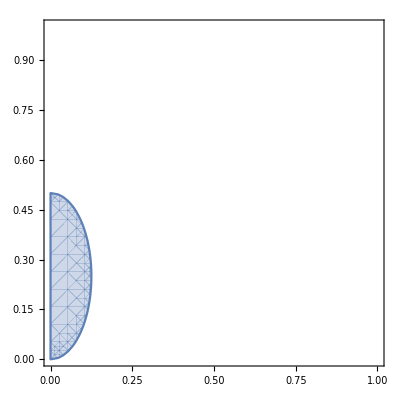

```mathematica
RegionPlot[(4α^2+β^2)/(2β)≤ 1/4,{α,0,1},{β,0,1}]
```

```mathematica
(14.14)/2.935
```

4.81772

```mathematica
(14.342+0.366+0.053)/2.875
```

5.13426

```mathematica
12.234/2.575
```

4.75107

```mathematica
1.8*10^9/15
```

1.2×10^8

```mathematica
ComplexExpand[Norm[B[1]+Subscript[θ, 1] IdentityMatrix[2]+Subscript[θ, 2] B[3]-Subscript[θ, 3] B[2],"Frobenius"]^2+Norm[B[2]+Subscript[θ, 2] IdentityMatrix[2]+Subscript[θ, 3] B[1]-Subscript[θ, 1] B[3],"Frobenius"]^2+Norm[B[3]+Subscript[θ, 3] IdentityMatrix[2]+Subscript[θ, 1] B[2]-Subscript[θ, 2] B[1],"Frobenius"]^2]
```

2 θ_1^2+2 θ_2^2+2 θ_3^2+2 √2 θ_1 b_(1,0)+b_(1,0)^2+θ_2^2 b_(1,0)^2+θ_3^2 b_(1,0)^2+b_(1,1)^2+θ_2^2 b_(1,1)^2+θ_3^2 b_(1,1)^2+b_(1,2)^2+θ_2^2 b_(1,2)^2+θ_3^2 b_(1,2)^2+b_(1,3)^2+θ_2^2 b_(1,3)^2+θ_3^2 b_(1,3)^2+2 √2 θ_2 b_(2,0)-2 θ_1 θ_2 b_(1,0) b_(2,0)+b_(2,0)^2+θ_1^2 b_(2,0)^2+θ_3^2 b_(2,0)^2-2 θ_1 θ_2 b_(1,1) b_(2,1)+b_(2,1)^2+θ_1^2 b_(2,1)^2+θ_3^2 b_(2,1)^2-2 θ_1 θ_2 b_(1,2) b_(2,2)+b_(2,2)^2+θ_1^2 b_(2,2)^2+θ_3^2 b_(2,2)^2-2 θ_1 θ_2 b_(1,3) b_(2,3)+b_(2,3)^2+θ_1^2 b_(2,3)^2+θ_3^2 b_(2,3)^2+2 √2 θ_3 b_(3,0)-2 θ_1 θ_3 b_(1,0) b_(3,0)-2 θ_2 θ_3 b_(2,0) b_(3,0)+b_(3,0)^2+θ_1^2 b_(3,0)^2+θ_2^2 b_(3,0)^2-2 θ_1 θ_3 b_(1,1) b_(3,1)-2 θ_2 θ_3 b_(2,1) b_(3,1)+b_(3,1)^2+θ_1^2 b_(3,1)^2+θ_2^2 b_(3,1)^2-2 θ_1 θ_3 b_(1,2) b_(3,2)-2 θ_2 θ_3 b_(2,2) b_(3,2)+b_(3,2)^2+θ_1^2 b_(3,2)^2+θ_2^2 b_(3,2)^2-2 θ_1 θ_3 b_(1,3) b_(3,3)-2 θ_2 θ_3 b_(2,3) b_(3,3)+b_(3,3)^2+θ_1^2 b_(3,3)^2+θ_2^2 b_(3,3)^2

```mathematica
NMaximize[{ComplexExpand[
Norm[B[1]+Subscript[θ, 1] σ[0]+Subscript[θ, 2] B[3]-Subscript[θ, 3] B[2],"Frobenius"]^2
+Norm[B[2]+Subscript[θ, 2] σ[0]+Subscript[θ, 3] B[1]-Subscript[θ, 1] B[3],"Frobenius"]^2
+Norm[B[3]+Subscript[θ, 3] σ[0]+Subscript[θ, 1] B[2]-Subscript[θ, 2] B[1],"Frobenius"]^2],Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2+Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2+Subscript[b, 3,0]^2+Subscript[b, 3,1]^2+Subscript[b, 3,2]^2+Subscript[b, 3,3]^2== 1&&{Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3]}∈Sphere[{0,0,0}]},
{Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3],Subscript[b, 2,0],Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3],Subscript[b, 3,0],Subscript[b, 3,1],Subscript[b, 3,2],Subscript[b, 3,3],Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3]}]
```

{4.,{b_(1,0)→-0.664379,b_(1,1)→-0.00156353,b_(1,2)→-0.0109204,b_(1,3)→-0.009945,b_(2,0)→-0.151916,b_(2,1)→0.00364768,b_(2,2)→-0.00667589,b_(2,3)→-0.00179153,b_(3,0)→-0.731454,b_(3,1)→0.000663519,b_(3,2)→0.011279,b_(3,3)→0.00938534,θ_1→-0.663883,θ_2→-0.151348,θ_3→-0.732361}}

```mathematica
Maximize[{Norm[Subscript[θ, 1] σ[0],"Frobenius"]^2+Norm[Subscript[θ, 2] σ[0],"Frobenius"]^2+Norm[Subscript[θ, 3] σ[0],"Frobenius"]^2,{Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3]}∈Sphere[{0,0,0}]},
{Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3]}]
```

{1,{θ_1→-1,θ_2→0,θ_3→0}}

```mathematica
Maximize[{ComplexExpand[
Norm[B[1]+0.2σ[0],"Frobenius"]^2
+Norm[B[2]-0.2B[3],"Frobenius"]^2
+Norm[B[3]+0.2B[2],"Frobenius"]^2],Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2+Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2+Subscript[b, 3,0]^2+Subscript[b, 3,1]^2+Subscript[b, 3,2]^2+Subscript[b, 3,3]^2==0.64},
{Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3],Subscript[b, 2,0],Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3],Subscript[b, 3,0],Subscript[b, 3,1],Subscript[b, 3,2],Subscript[b, 3,3]}]
```

{1.,{b_(1,0)→0.800002,b_(1,1)→2.28349×10^-7,b_(1,2)→1.84072×10^-7,b_(1,3)→-2.89613×10^-7,b_(2,0)→1.30014×10^-6,b_(2,1)→1.04681×10^-6,b_(2,2)→-2.70844×10^-7,b_(2,3)→-8.02796×10^-7,b_(3,0)→1.38857×10^-6,b_(3,1)→9.31752×10^-7,b_(3,2)→1.36181×10^-6,b_(3,3)→-6.88223×10^-7}}

```mathematica
Sqrt[1.44]
```

1.2

```mathematica
ComplexExpand[
Norm[B[1]+θ σ[0],"Frobenius"]^2
+Norm[B[2]-θ B[3],"Frobenius"]^2
+Norm[B[3]+θ B[2],"Frobenius"]^2]
```

θ^2+2 θ b_(1,0)+b_(1,0)^2+b_(1,1)^2+b_(1,2)^2+b_(1,3)^2+b_(2,0)^2+θ^2 b_(2,0)^2+b_(2,1)^2+θ^2 b_(2,1)^2+b_(2,2)^2+θ^2 b_(2,2)^2+b_(2,3)^2+θ^2 b_(2,3)^2+b_(3,0)^2+θ^2 b_(3,0)^2+b_(3,1)^2+θ^2 b_(3,1)^2+b_(3,2)^2+θ^2 b_(3,2)^2+b_(3,3)^2+θ^2 b_(3,3)^2

```mathematica
Collect[%356,θ]
```

2 θ b_(1,0)+b_(1,0)^2+b_(1,1)^2+b_(1,2)^2+b_(1,3)^2+b_(2,0)^2+b_(2,1)^2+b_(2,2)^2+b_(2,3)^2+b_(3,0)^2+b_(3,1)^2+b_(3,2)^2+b_(3,3)^2+θ^2 (1+b_(2,0)^2+b_(2,1)^2+b_(2,2)^2+b_(2,3)^2+b_(3,0)^2+b_(3,1)^2+b_(3,2)^2+b_(3,3)^2)

```mathematica
9*14*27
```

3402

```mathematica
133.971/3096.897
```

0.0432598

```mathematica
20.653/743.481
```

0.0277788

```mathematica
pic2=Module[{n=2},Show[RegionPlot[Callout[(0<α<β/2^n&&(4^n α^2+β^2)/(2β)≤ 1/(2^(n^2+n)α^(n-1)))||(α≥ β/2^n>0&&α≤ 1/2^(n+2)),"noise removal",{0.2,0.4}],{α,0,0.6},{β,0,0.6},PlotStyle->Directive[Opacity[0.3],Orange],FrameLabel->{"α","β"}],
RegionPlot[Callout[α+β≤ 1/4^n,"abosulte convergence",{0.3,0.15}],{α,0,0.6},{β,0,0.6}]]]
```

-Graphics-

```mathematica
Export["~/Desktop/DD/region2.pdf",pic2]
```

~/Desktop/DD/region2.pdf

```mathematica
pic3=Module[{n=3},Show[RegionPlot[Callout[(0<α<β/2^n&&(4^n α^2+β^2)/(2β)≤ 1/(2^(n^2+n)α^(n-1)))||(α≥ β/2^n>0&&α≤ 1/2^(n+2)),"noise removal",{0.2,0.4}],{α,0,0.1},{β,0,0.6},PlotStyle->Directive[Opacity[0.3],Orange],FrameLabel->{"α","β"}],
RegionPlot[Callout[α+β≤ 1/4^n,"abosulte convergence",{0.3,0.15}],{α,0,0.1},{β,0,0.6}]]]
```

-Graphics-

```mathematica
Export["~/Desktop/DD/region3.pdf",pic3]
```

~/Desktop/DD/region3.pdf

```mathematica
SystemOpen["~/Desktop/DD/region3.pdf"]
```

```mathematica
1/2^(n+2)/.n->3
```

1/32

```mathematica
1/4^n/.n->3
```

1/64

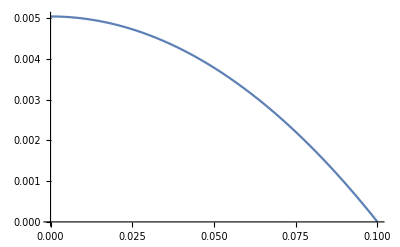

```mathematica
Plot[Evaluate[{1-((1+β^2-2βc^2)/(1-β^2))^(1/4)}/.βc->0.1],{β,0,0.1}]
```

```mathematica
Reduce[(1-β^2)((1+p^4)/2)>1-βc^2&&0<βc<1/(√2)&&0<β<1,p]
```

0<βc<1/(√2)&&0<β<1&&(p<-((-1-β^2+2 βc^2)/(-1+β^2))^(1/4)||p>((-1-β^2+2 βc^2)/(-1+β^2))^(1/4))

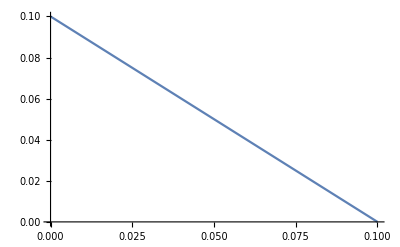

```mathematica
Plot[Evaluate[{βc-β}/.βc->0.1],{β,0,0.1}]
```

```mathematica
Bt[1]=β B[1]+Subscript[θ, 1] IdentityMatrix[2]+β(Subscript[θ, 2] B[3]-Subscript[θ, 3] B[2])
```

{{θ_1+β ((b_(1,0))/(√2)+(b_(1,3))/(√2))+β (-θ_3 ((b_(2,0))/(√2)+(b_(2,3))/(√2))+θ_2 ((b_(3,0))/(√2)+(b_(3,3))/(√2))),β ((b_(1,1))/(√2)-(ⅈ b_(1,2))/(√2))+β (-θ_3 ((b_(2,1))/(√2)-(ⅈ b_(2,2))/(√2))+θ_2 ((b_(3,1))/(√2)-(ⅈ b_(3,2))/(√2)))},{β ((b_(1,1))/(√2)+(ⅈ b_(1,2))/(√2))+β (-θ_3 ((b_(2,1))/(√2)+(ⅈ b_(2,2))/(√2))+θ_2 ((b_(3,1))/(√2)+(ⅈ b_(3,2))/(√2))),θ_1+β ((b_(1,0))/(√2)-(b_(1,3))/(√2))+β (-θ_3 ((b_(2,0))/(√2)-(b_(2,3))/(√2))+θ_2 ((b_(3,0))/(√2)-(b_(3,3))/(√2)))}}

```mathematica
Bt[2]=β B[2]+Subscript[θ, 2] IdentityMatrix[2]+β(Subscript[θ, 3] B[1]-Subscript[θ, 1] B[3])
```

{{θ_2+β ((b_(2,0))/(√2)+(b_(2,3))/(√2))+β (θ_3 ((b_(1,0))/(√2)+(b_(1,3))/(√2))-θ_1 ((b_(3,0))/(√2)+(b_(3,3))/(√2))),β ((b_(2,1))/(√2)-(ⅈ b_(2,2))/(√2))+β (θ_3 ((b_(1,1))/(√2)-(ⅈ b_(1,2))/(√2))-θ_1 ((b_(3,1))/(√2)-(ⅈ b_(3,2))/(√2)))},{β ((b_(2,1))/(√2)+(ⅈ b_(2,2))/(√2))+β (θ_3 ((b_(1,1))/(√2)+(ⅈ b_(1,2))/(√2))-θ_1 ((b_(3,1))/(√2)+(ⅈ b_(3,2))/(√2))),θ_2+β ((b_(2,0))/(√2)-(b_(2,3))/(√2))+β (θ_3 ((b_(1,0))/(√2)-(b_(1,3))/(√2))-θ_1 ((b_(3,0))/(√2)-(b_(3,3))/(√2)))}}

```mathematica
Bt[3]=β B[3]+Subscript[θ, 3] IdentityMatrix[2]+β(Subscript[θ, 1] B[2]-Subscript[θ, 2] B[1])
```

{{θ_3+β (-θ_2 ((b_(1,0))/(√2)+(b_(1,3))/(√2))+θ_1 ((b_(2,0))/(√2)+(b_(2,3))/(√2)))+β ((b_(3,0))/(√2)+(b_(3,3))/(√2)),β (-θ_2 ((b_(1,1))/(√2)-(ⅈ b_(1,2))/(√2))+θ_1 ((b_(2,1))/(√2)-(ⅈ b_(2,2))/(√2)))+β ((b_(3,1))/(√2)-(ⅈ b_(3,2))/(√2))},{β (-θ_2 ((b_(1,1))/(√2)+(ⅈ b_(1,2))/(√2))+θ_1 ((b_(2,1))/(√2)+(ⅈ b_(2,2))/(√2)))+β ((b_(3,1))/(√2)+(ⅈ b_(3,2))/(√2)),θ_3+β (-θ_2 ((b_(1,0))/(√2)-(b_(1,3))/(√2))+θ_1 ((b_(2,0))/(√2)-(b_(2,3))/(√2)))+β ((b_(3,0))/(√2)-(b_(3,3))/(√2))}}

```mathematica
Bt[0]=α B[0]
```

{{(α b_(0,3))/(√2),α ((b_(0,1))/(√2)-(ⅈ b_(0,2))/(√2))},{α ((b_(0,1))/(√2)+(ⅈ b_(0,2))/(√2)),-(α b_(0,3))/(√2)}}

```mathematica
beta2=Norm[-4ⅈ cm[Bt[0],Bt[1]],"Frobenius"]^2+Norm[-2ⅈ cm[Bt[0],Bt[2]]+2am[Bt[1],Bt[3]],"Frobenius"]^2//ComplexExpand
```

32 θ_1^2 θ_3^2-32 √2 β θ_1^2 θ_2 θ_3 b_(1,0)+32 √2 β θ_1 θ_3^2 b_(1,0)+16 β^2 θ_1^2 θ_2^2 b_(1,0)^2-64 β^2 θ_1 θ_2 θ_3 b_(1,0)^2+16 β^2 θ_3^2 b_(1,0)^2+1985+16 β^4 θ_2^2 b_(3,2)^2 b_(3,3)^2+16 β^4 θ_2 b_(1,3) b_(3,3)^3-16 β^4 θ_2^3 b_(1,3) b_(3,3)^3+16 β^4 θ_1 θ_2^2 b_(2,3) b_(3,3)^3-16 β^4 θ_2 θ_3 b_(2,3) b_(3,3)^3+8 β^4 θ_2^2 b_(3,3)^4
 |  |  |  |

```mathematica
NMaximize[{beta2/.{α->0.1,β->0.3},Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2+Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2+Subscript[b, 3,0]^2+Subscript[b, 3,1]^2+Subscript[b, 3,2]^2+Subscript[b, 3,3]^2== 1&&Subscript[b, 0,1]^2+Subscript[b, 0,2]^2+Subscript[b, 0,3]^2==1&&Subscript[θ, 1]^2+Subscript[θ, 2]^2+Subscript[θ, 3]^2==0.1^2},{Subscript[b, 0,1],Subscript[b, 0,2],Subscript[b, 0,3],Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3],Subscript[b, 2,0],Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3],Subscript[b, 3,0],Subscript[b, 3,1],Subscript[b, 3,2],Subscript[b, 3,3],Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3]}]
```

{0.112919,{b_(0,1)→0.804436,b_(0,2)→0.260351,b_(0,3)→-0.533947,b_(1,0)→0.464504,b_(1,1)→0.235392,b_(1,2)→0.214445,b_(1,3)→0.457434,b_(2,0)→0.000111079,b_(2,1)→0.0508081,b_(2,2)→-0.100576,b_(2,3)→0.0275001,b_(3,0)→-0.481536,b_(3,1)→-0.208143,b_(3,2)→-0.170323,b_(3,3)→-0.394881,θ_1→0.0693068,θ_2→-5.88625×10^-10,θ_3→-0.0720872}}

```mathematica
NMaximize[{beta2/.{α->0.1,β->0.1},Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2+Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2+Subscript[b, 3,0]^2+Subscript[b, 3,1]^2+Subscript[b, 3,2]^2+Subscript[b, 3,3]^2== 1&&Subscript[b, 0,1]^2+Subscript[b, 0,2]^2+Subscript[b, 0,3]^2==1&&Subscript[θ, 1]^2+Subscript[θ, 2]^2+Subscript[θ, 3]^2==0.01},{Subscript[b, 0,1],Subscript[b, 0,2],Subscript[b, 0,3],Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3],Subscript[b, 2,0],Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3],Subscript[b, 3,0],Subscript[b, 3,1],Subscript[b, 3,2],Subscript[b, 3,3],Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3]}]
```

{0.00546682,{b_(0,1)→0.961343,b_(0,2)→-0.013846,b_(0,3)→-0.275006,b_(1,0)→-1.14395×10^-12,b_(1,1)→0.225652,b_(1,2)→0.487985,b_(1,3)→0.764246,b_(2,0)→-5.05879×10^-14,b_(2,1)→-0.0543297,b_(2,2)→0.169982,b_(2,3)→-0.19848,b_(3,0)→0.235882,b_(3,1)→-5.63398×10^-13,b_(3,2)→-1.16071×10^-12,b_(3,3)→-1.96537×10^-12,θ_1→-2.97284×10^-13,θ_2→-2.8933×10^-13,θ_3→0.1}}

```mathematica
NMaximize[{beta2/.{α->0,β->0.1},Subscript[b, 1,0]^2+Subscript[b, 1,1]^2+Subscript[b, 1,2]^2+Subscript[b, 1,3]^2+Subscript[b, 2,0]^2+Subscript[b, 2,1]^2+Subscript[b, 2,2]^2+Subscript[b, 2,3]^2+Subscript[b, 3,0]^2+Subscript[b, 3,1]^2+Subscript[b, 3,2]^2+Subscript[b, 3,3]^2== 1&&Subscript[b, 0,1]^2+Subscript[b, 0,2]^2+Subscript[b, 0,3]^2==1&&Subscript[θ, 1]^2+Subscript[θ, 2]^2+Subscript[θ, 3]^2==0.01},{Subscript[b, 0,1],Subscript[b, 0,2],Subscript[b, 0,3],Subscript[b, 1,0],Subscript[b, 1,1],Subscript[b, 1,2],Subscript[b, 1,3],Subscript[b, 2,0],Subscript[b, 2,1],Subscript[b, 2,2],Subscript[b, 2,3],Subscript[b, 3,0],Subscript[b, 3,1],Subscript[b, 3,2],Subscript[b, 3,3],Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3]}]
```

{0.00224021,{b_(0,1)→0.823638,b_(0,2)→-0.387909,b_(0,3)→-0.4137,b_(1,0)→0.437016,b_(1,1)→2.20326×10^-31,b_(1,2)→-8.47409×10^-32,b_(1,3)→-1.79882×10^-31,b_(2,0)→1.27608×10^-32,b_(2,1)→-0.0648521,b_(2,2)→-0.0264323,b_(2,3)→-0.0557279,b_(3,0)→7.97335×10^-32,b_(3,1)→-0.648521,b_(3,2)→-0.264323,b_(3,3)→-0.557279,θ_1→0.1,θ_2→-2.07037×10^-33,θ_3→2.00056×10^-32}}

```mathematica
B[0]/.%561[[2]]//MatrixForm
```

(-0.194458 | 0.679772+0.0097906 ⅈ
0.679772-0.0097906 ⅈ | 0.194458)

```mathematica
am[B[0],B[1]-Subscript[θ, 3] B[2]+Subscript[θ, 2] B[3]]/.%561[[2]]//MatrixForm
```

(3.35537×10^-13+0. ⅈ | -1.16052×10^-12-1.67141×10^-14 ⅈ
-1.16052×10^-12+1.67141×10^-14 ⅈ | -3.28432×10^-13+0. ⅈ)

```mathematica
am[B[0],B[2]+Subscript[θ, 3] B[1]-Subscript[θ, 1] B[3]]/.%562[[2]]//MatrixForm
```

(1.94739×10^-9+0. ⅈ | -2.91281×10^-9+9.42715×10^-10 ⅈ
-2.91281×10^-9-9.42715×10^-10 ⅈ | -1.91938×10^-9+0. ⅈ)

```mathematica
cm[B[1]-Subscript[θ, 3] B[2]+Subscript[θ, 2] B[3],B[3]+Subscript[θ, 1] B[2]-Subscript[θ, 2] B[1]]/.%577[[2]]
```

{{0.-1.14326×10^-31 ⅈ,1.25497×10^-31+4.7091×10^-32 ⅈ},{-1.25497×10^-31+4.7091×10^-32 ⅈ,0.+1.14326×10^-31 ⅈ}}

```mathematica
B[2]+Subscript[θ, 3] B[1]/.%561[[2]]
```

{{-0.086306,-0.0224609-0.154702 ⅈ},{-0.0224609+0.154702 ⅈ,0.086306}}

```mathematica
Bt[2]//MatrixForm
```

(θ_2+β ((b_(2,0))/(√2)+(b_(2,3))/(√2))+β (θ_3 ((b_(1,0))/(√2)+(b_(1,3))/(√2))-θ_1 ((b_(3,0))/(√2)+(b_(3,3))/(√2))) | β ((b_(2,1))/(√2)-(ⅈ b_(2,2))/(√2))+β (θ_3 ((b_(1,1))/(√2)-(ⅈ b_(1,2))/(√2))-θ_1 ((b_(3,1))/(√2)-(ⅈ b_(3,2))/(√2)))
β ((b_(2,1))/(√2)+(ⅈ b_(2,2))/(√2))+β (θ_3 ((b_(1,1))/(√2)+(ⅈ b_(1,2))/(√2))-θ_1 ((b_(3,1))/(√2)+(ⅈ b_(3,2))/(√2))) | θ_2+β ((b_(2,0))/(√2)-(b_(2,3))/(√2))+β (θ_3 ((b_(1,0))/(√2)-(b_(1,3))/(√2))-θ_1 ((b_(3,0))/(√2)-(b_(3,3))/(√2))))